```mathematica
fnspek=FileNames["*","C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\SpekMas\\PG\\Spektra"];
DataSpek=Import[#,"Table",NumberPoint->","]&/@ fnspek;
```

```mathematica
fnspek
```

{C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\210416AfterBA,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\210416AfterOxygenInjection,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_14-37-48.txt,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_14-38-11.txt,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_14-45-03008,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_14-50-50012,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_14-57-45016,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-04-41012td05,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-20-20012td20,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-26-510012td002ms15,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-32-03.txt,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-32-10BAON,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-55-04potlenie,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-21_11-03-33.txt}

```mathematica
fnspek[[8]]
```

C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-04-41012td05

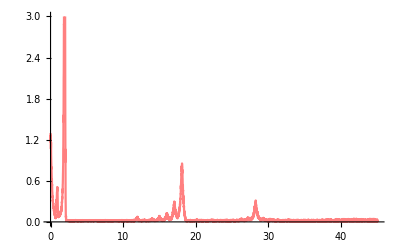
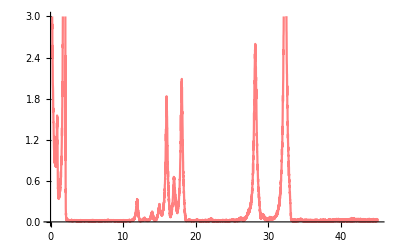
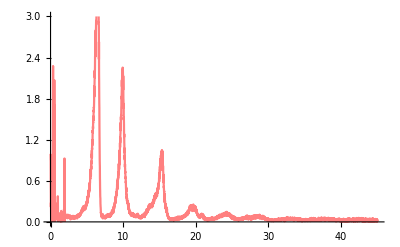
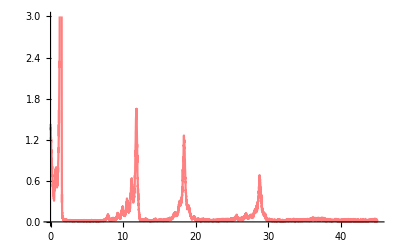
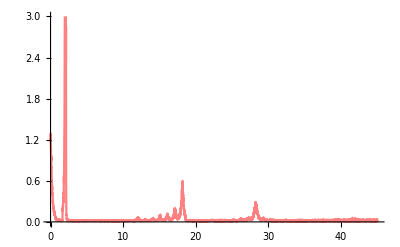
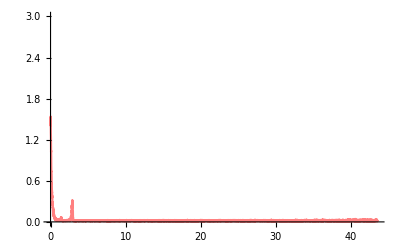
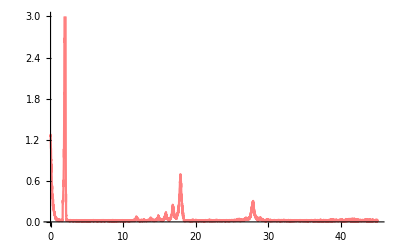
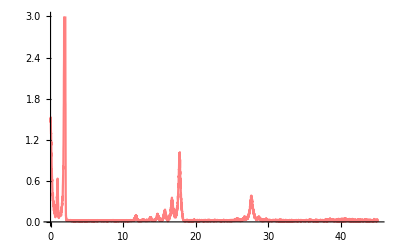
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SpekPlots=ListLinePlot[#,PlotRange-> {0,3},PlotStyle->Pink]&/@DataSpek
```

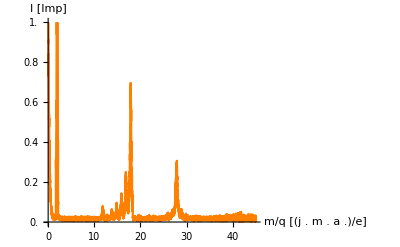

```mathematica
plocik=ListLinePlot[DataSpek[[8]],PlotRange->{0,1},PlotStyle->Orange,Ticks->{Range[0,45,2],Range[0,1,0.1]},AxesLabel->{"m/q [(j . m . a .)/e]","I [Imp]"}]
```

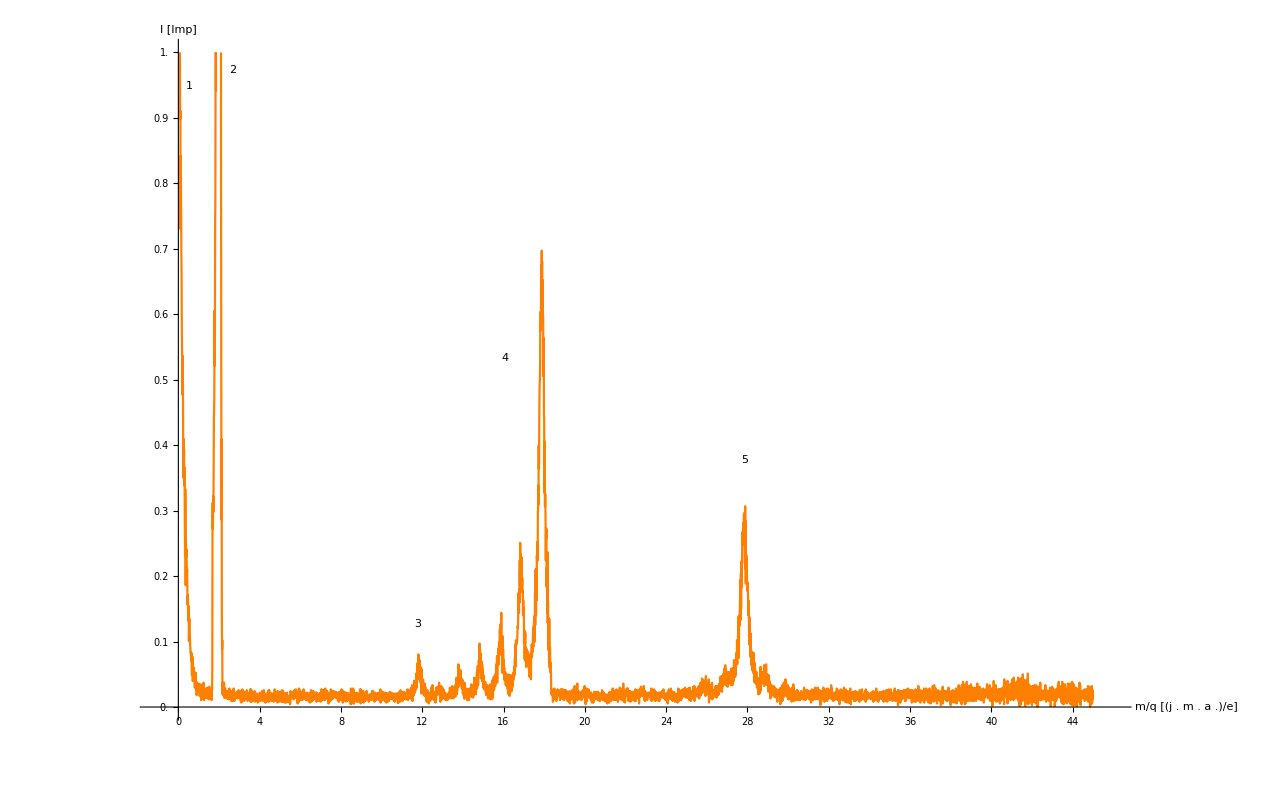

-Graphics-

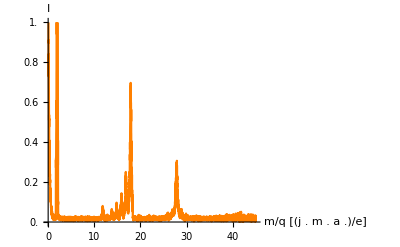

```mathematica
plocik=ListLinePlot[DataSpek[[8]],PlotRange->{0,1},PlotStyle->Orange,Ticks->{Range[0,45,2],Range[0,1,0.1]},AxesLabel->{"m/q [(j . m . a .)/e]","I "}]
```

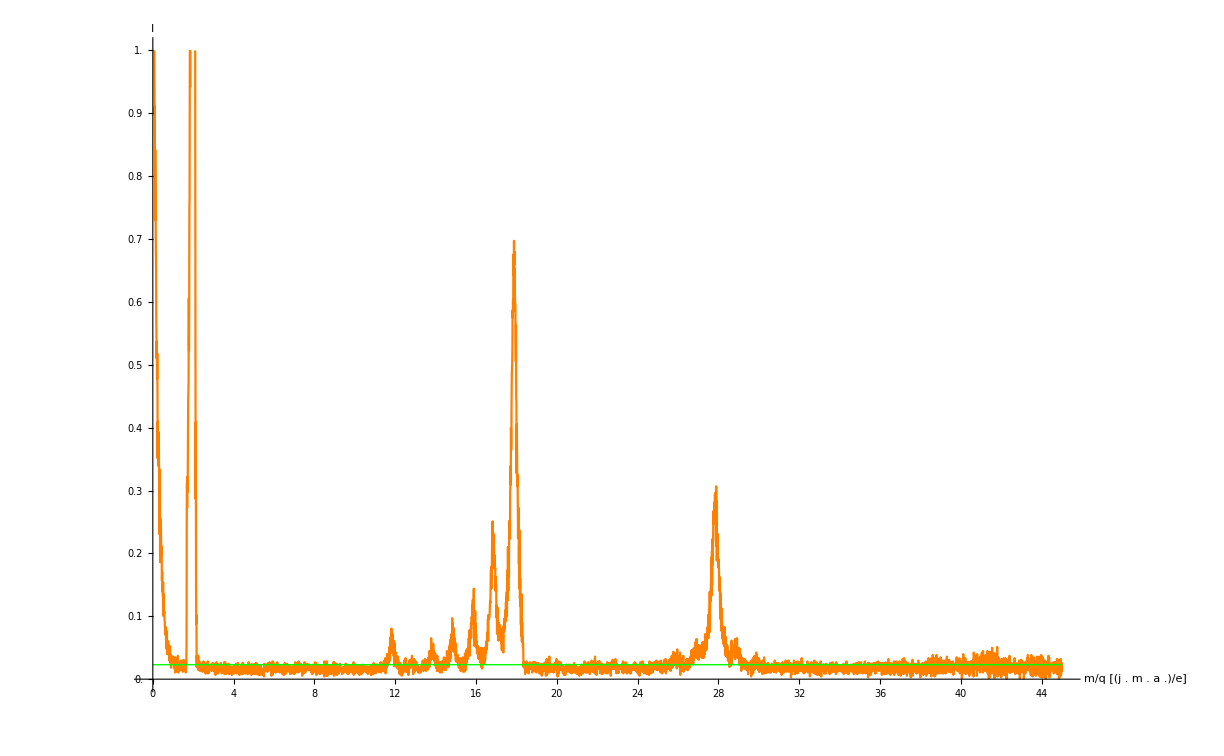

```mathematica
Show[plocik,Plot[0.023,{x,0,45},PlotStyle->{Green,Thick}]]
```

```mathematica
cut={{1.6,2.3},{11.4,12.3},{13.4,14.2},{14.5,15.2},{15.5,16.2},{16.4,17.26},{17.26,18.4},{27.1,28.7}}

Sum[(cut[[i]][[2]]-cut[[i]][[1]])/8,{i,1,5}]+(cut[[6]][[2]]-cut[[6]][[1]])/16+(cut[[7]][[2]]-cut[[7]][[1]])/8
Transpose[cut]//TeXForm
```

{{1.6,2.3},{11.4,12.3},{13.4,14.2},{14.5,15.2},{15.5,16.2},{16.4,17.26},{17.26,18.4},{27.1,28.7}}

0.67125

\left(
\begin{array}{cccccccc}
 1.6 & 11.4 & 13.4 & 14.5 & 15.5 & 16.4 & 17.26 & 27.1 \\
 2.3 & 12.3 & 14.2 & 15.2 & 16.2 & 17.26 & 18.4 & 28.7 \\
\end{array}
\right)

```mathematica
cut[[1]][[1]]
```

1.6

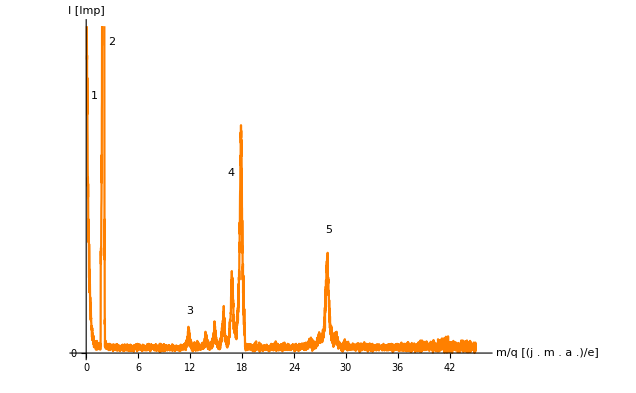

-Graphics-

-Graphics-

C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\spectra_2016-04-14_15-32-10BAON

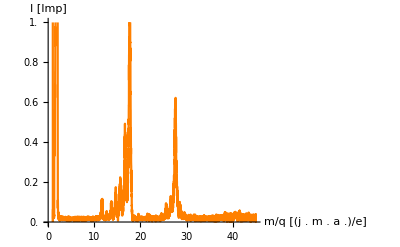

```mathematica
fnspek[[Length[DataSpek]-2]]
ListLinePlot[DataSpek[[Length[DataSpek]-2]],PlotRange->{0,1},PlotStyle->Orange,Ticks->{Range[0,45,2],Range[0,1,0.1]},AxesLabel->{"m/q [(j . m . a .)/e]","I [Imp]"}]
```

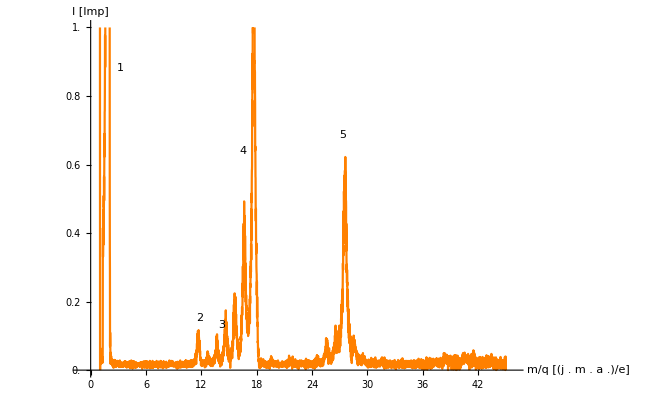

-Graphics-

C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Spektra\210416AfterOxygenInjection

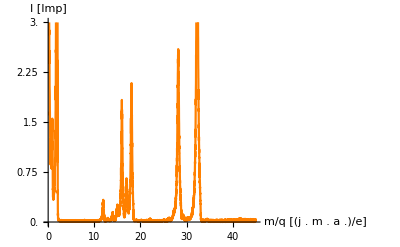

```mathematica
fnspek[[2]]
ListLinePlot[DataSpek[[2]],PlotRange->{0,3},PlotStyle->Orange,Ticks->{Range[0,45,2],Range[0,3,0.25]},AxesLabel->{"m/q [(j . m . a .)/e]","I [Imp]"}]
```

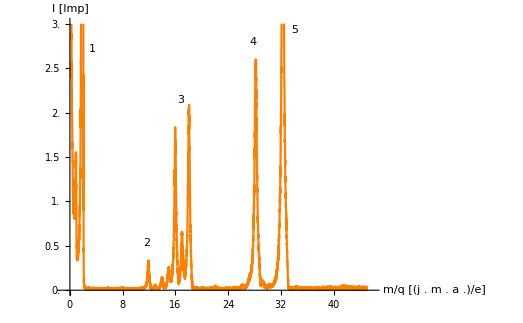

-Graphics-

```mathematica
fntime=FileNames["*","C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\SpekMas\\PG\\Time"];
DataTime=Import[#,"Table",NumberPoint->","]&/@ fntime;
```

```mathematica
fntime
```

{C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-14_15-36-031,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-14_15-39-162,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-14_15-41-473,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-14_15-49-26tlen,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-21_11-21-50.txt,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-21_11-34-17tlo1,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-21_11-59-02tlo2,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-21_12-21-52wodor,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-21_12-38-05pik,C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\SpekMas\PG\Time\time_dependence_2016-04-21_12-43-4932}

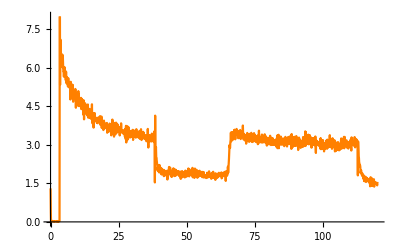
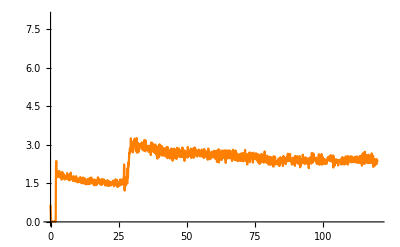
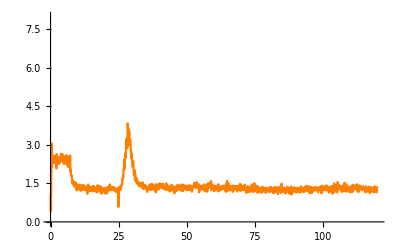
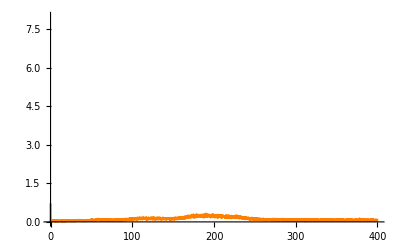
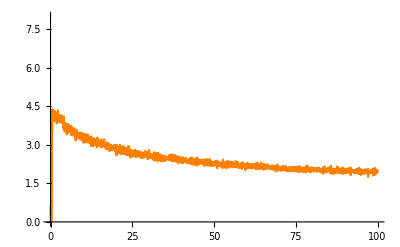
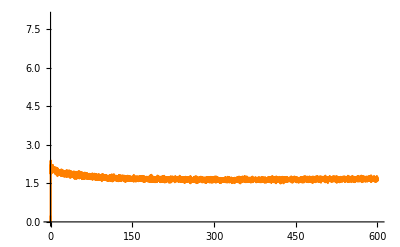
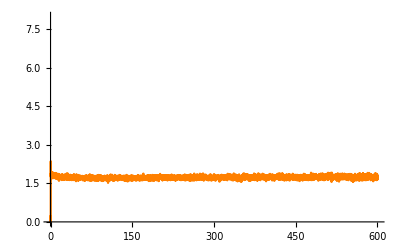
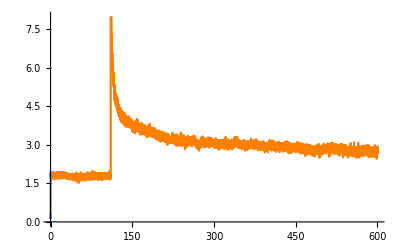

```mathematica
TimePlots=ListLinePlot[#,PlotRange-> {0,8},PlotStyle->Orange]&/@DataTime
```

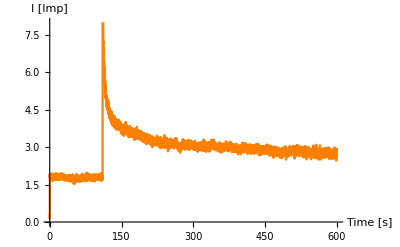

```mathematica
ListLinePlot[DataTime[[Length[DataTime]-2]],AxesLabel->{"Time [s]","I [Imp]"},PlotRange-> {0,8},PlotStyle->Orange]
```

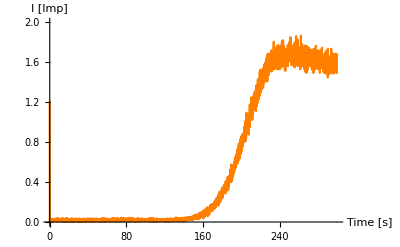

```mathematica
ListLinePlot[DataTime[[Length[DataTime]]],AxesLabel->{"Time [s]","I [Imp]"},PlotRange-> {0,2},PlotStyle->Orange]
```

```mathematica
ListLinePlot[DataTime[[Length[DataTime]]],AxesLabel->{"Time [s]","I [Imp]"},PlotRange-> {0,2},PlotStyle->Orange]
```

-Graphics-

By policzyć rozdzielczość, zmierzymy szerokość peaków w połowie ich wysokości.

```mathematica
FindMaxinInterval[Dane_,Int0_,IntF_]:=MaximalBy[Select[Dane[[2;;Length[Dane]]],#[[1]]≥Int0&&#[[1]]<=IntF&],Last]
```

```mathematica
GetResolution[int_]:=Module[{max,back=0.023,halfdif=0,a,b},max=FindMaxinInterval[DataSpek[[8]],int[[1]],int[[2]]];
halfdif=(max[[1]][[2]]-back)/2;
a=MinimalBy[{#[[1]],Abs[#[[2]]-halfdif]}&/@Select[DataSpek[[8]],#[[1]]≥int[[1]]&&#[[1]]≤max[[1]][[1]]&],Last];
b=MinimalBy[{#[[1]],Abs[#[[2]]-halfdif]}&/@Select[DataSpek[[8]],#[[1]]≥max[[1]][[1]]&&#[[1]]≤int[[2]]&],Last];Return[b[[1]][[1]]-a[[1]][[1]]]]
```

```mathematica
Res=GetResolution/@cut
```

{0.14,0.55,0.59,0.34,0.33,0.39,0.3,0.43}

```mathematica
Sum[Res[[i]],{i,1,Length[Res]}]/Length[Res]
```

0.38375